```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

## Peak Theory

```mathematica
npeak=16;
NL=256;
L=10^-12;(*Mpc*)
kpeak=2π npeak/NL;
```

### Monochromatic

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nnu2PT[nu2_,ks_]=ks^3/(6π)^(3/2) f[nu2] 1/Sqrt[2π] Exp[-nu2^2/2];
```

```mathematica
Cm[nu2_,As_]=2/3(1-(1+xm Sinc'[xm]Sqrt[As]nu2)^2)/.{xm->2.74};
```

```mathematica
dlnMdmu2[nu2_,As_]=2Sqrt[As]Sinc[xm]+γ/(Cm[nu2,As]-Cth)D[Cm[nu2,As], nu2]/.{Cth->0.533,γ->0.36,xm->2.74}//Simplify;
```

```mathematica
nPBHpk[nu2_,ks_,As_]=nnu2PT[nu2,ks]/Abs[dlnMdmu2[nu2,As]];
```

```mathematica
Mpk[nu2_,As_]=xm^2 Exp[2Sqrt[As]Sinc[xm]nu2](Cm[nu2,As]-Cth)^γ/.{Cth->0.533,γ->0.36,xm->2.74};
Mks[ks_]=(NL/L ks/(1.56 10^13))^-2;
```

```mathematica
fPBHpk[nu2_,ks_,As_]=Mks[ks] Mpk[nu2,As] nPBHpk[nu2,ks,As]/(3.95 10^-20);
```

```mathematica
Mkpeak=Mks[kpeak]
```

0.0240796

```mathematica
Azeta=3.625 10^-3;
nu2th=nu2/.FindRoot[Cm[nu2,Azeta]==0.533,{nu2,8}];
fPBHpkList=Table[{Mkpeak Mpk[nu2th+10^dlnnu2,Azeta],fPBHpk[nu2th+10^dlnnu2,kpeak,Azeta]},{dlnnu2,-5,1/2,10^-2}];
```

```mathematica
Mmin=First[fPBHpkList][[1]]
Mmax=Last[fPBHpkList][[1]]
```

0.00102593

0.0943306

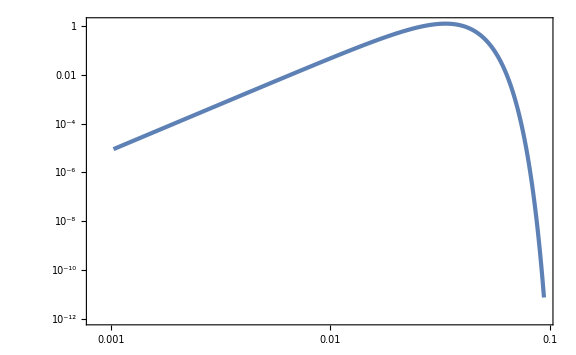

```mathematica
ListLogLogPlot[fPBHpkList]
```

```mathematica
fPBHpkint[M_]=Interpolation[fPBHpkList][M];
NIntegrate[fPBHpkint[M]/M,{M,Mmin,Mmax}]
```

1.00416

```mathematica
Export["data/fPBH_pk_mono.csv",fPBHpkList];
```

## Importance Sampling

```mathematica
npeak=16;
NL=256;
L=10^-12;(*Mpc*)
kpeak=2π npeak/NL;
```

### Monochromatic

```mathematica
σ2=kpeak^2;
```

```mathematica
Nsim=100;
nu2k3tList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1].DiagonalMatrix[{1/σ2,1/kpeak}];
```

```mathematica
Dnu2=HistogramList[nu2k3tList[[All,1]]][[1,2]]-HistogramList[nu2k3tList[[All,1]]][[1,1]];
nu2min=Mean[HistogramList[nu2k3tList[[All,1]]][[1,1;;2]]];
nnu2IS=Table[{nu2min+Dnu2(i-1),(HistogramList[nu2k3tList[[All,1]]][[2,i]])/(Dnu2 Nsim NL^3)},{i,Length[HistogramList[nu2k3tList[[All,1]]][[2]]]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nnu2PT[nu2_,ks_]=ks^3/(6π)^(3/2) f[nu2] 1/Sqrt[2π] Exp[-nu2^2/2];
```

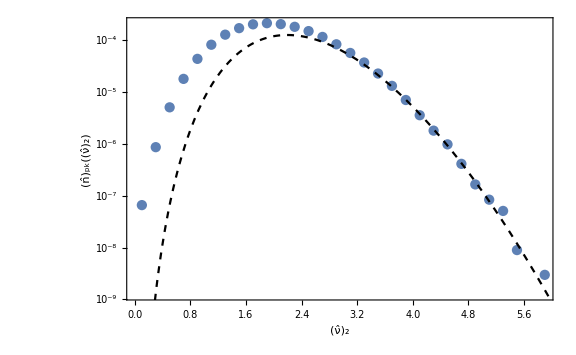

```mathematica
Show[ListLogPlot[nnu2IS,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]]}],LogPlot[nnu2PT[nu2,kpeak],{nu2,0,6},PlotStyle->{Dashed,Black}]]
```

```mathematica
ISdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[ISdata]
```

1000

```mathematica
Cmdata=Map[{#[[6]],Log10[Exp[#[[7]]]]}&,ISdata];
```

```mathematica
DensityHistogram[Cmdata,ChartLegends->Automatic,FrameLabel->{Subscript[𝒞, "m"],"log_10𝒲"},GridLines->{{0.533},None}]
```

-Graphics-

```mathematica
Dnu2IS=HistogramList[ISdata[[All,2]]/σ2][[1,2]]-HistogramList[ISdata[[All,2]]/σ2][[1,1]]
```

1/2

```mathematica
nu2minIS=HistogramList[ISdata[[All,2]]/σ2][[1,1]]
nu2maxIS=HistogramList[ISdata[[All,2]]/σ2][[1]]//Last
```

5

25/2

```mathematica
nu2binning[nu2_]:=Select[ISdata,nu2<=(#[[2]])/σ2<nu2+Dnu2IS&]
k33sum[mu2_]:=Total[(nu2binning[mu2][[All,3]])^3]
```

```mathematica
nSnu2List=Table[{nu2+Dnu2IS/2,k33sum[nu2]/(Ntot Dnu2IS)},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
```

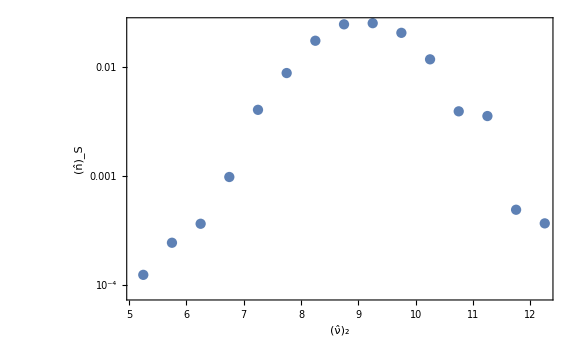

```mathematica
ListLogPlot[nSnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wnu2List=Table[{nu2,If[Length[nu2binning[nu2]]>1,Exp[Mean[nu2binning[nu2][[All,7]]]+Variance[nu2binning[nu2][[All,7]]]/2],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
wnu2errp=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
wnu2errm=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[-Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];;
```

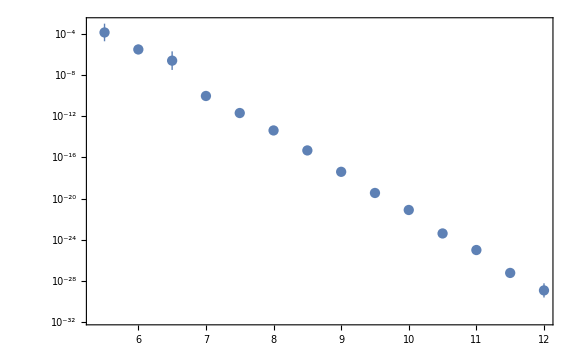

```mathematica
ListLogPlot[Table[{wnu2List[[i,1]],wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[wnu2List]}],Joined->False]
```

```mathematica
nTnu2List=Table[{nSnu2List[[i,1]],nSnu2List[[i,2]]wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[nSnu2List]}];
```

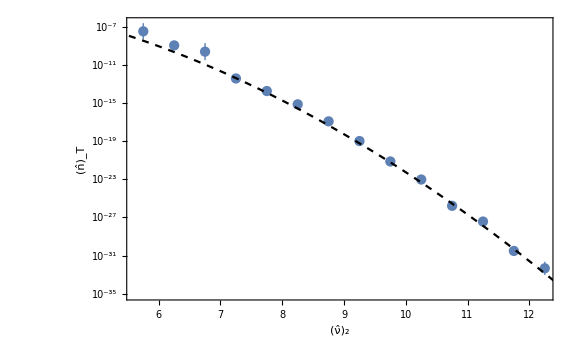

```mathematica
Show[ListLogPlot[nTnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "T"]}],LogPlot[nnu2PT[nu2,kpeak],{nu2,4,15},PlotStyle->{Black,Dashed}]]
```

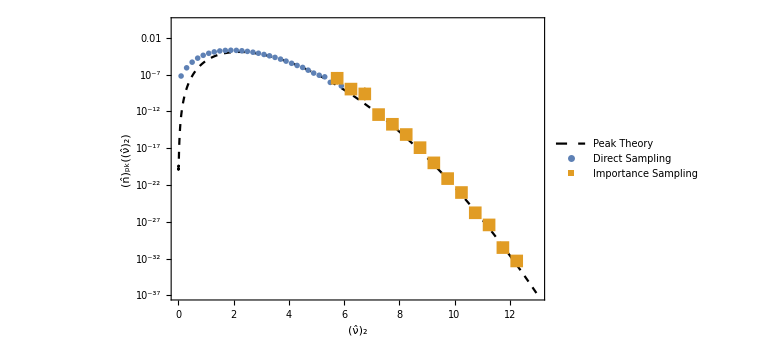

```mathematica
Show[LogPlot[nnu2PT[nu2,kpeak],{nu2,0,13},PlotStyle->{Black,Dashed},FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]]},PlotLegends->Placed[LineLegend[{"Peak Theory"},LegendMarkerSize->20,LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.3},Right}]],
ListLogPlot[nnu2IS,Joined->False,PlotMarkers->Style["●",Color[1]],PlotLegends->Placed[PointLegend[{"Direct Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.2},Right}]],ListLogPlot[nTnu2List,Joined->False,PlotMarkers->Style["■",Color[2],13],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.1},Right}]]]
```

```mathematica
MPBH[xm_,zetam_,Cm_]=xm^2 E^(2zetam)(Cm-Cth)^γ/.{γ->0.36,Cth->0.533};
```

```mathematica
Mks[ks_]=(NL/L ks/(1.56 10^13))^-2;
```

```mathematica
MPBHList=Map[{#[[3]],MPBH[#[[4]],#[[5]],#[[6]]]Mks[kpeak],#[[7]]}&,Select[ISdata,#[[6]]>0.533&]];
```

```mathematica
DlnM=HistogramList[Log[MPBHList[[All,2]]]][[1,2]]-HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
```

1/10

```mathematica
lnMmin=HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
lnMmax=HistogramList[Log[MPBHList[[All,2]]]][[1]]//Last
```

-26/5

-23/10

```mathematica
lnMbinning[lnM_]:=Select[MPBHList,lnM<=Log[#[[2]]]<lnM+DlnM&];
k33sumlnM[lnM_]:=Total[(lnMbinning[lnM][[All,1]])^3]
```

```mathematica
nSlnMList=Table[{lnM+DlnM/2,k33sumlnM[lnM]/(Ntot DlnM)},{lnM,lnMmin,lnMmax,DlnM}];
```

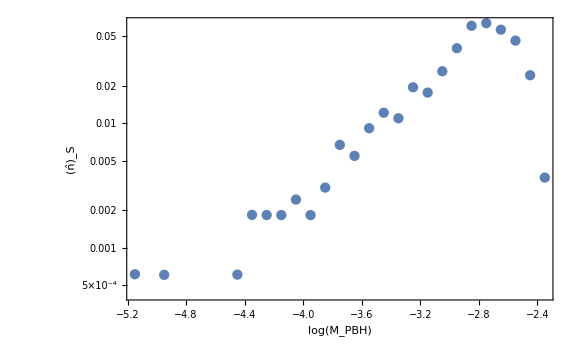

```mathematica
ListLogPlot[nSlnMList,Joined->False,FrameLabel->{Log[Subscript[M, PBH]],Subscript[OverHat[n], "S"]}]
```

```mathematica
wlnMList=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Exp[Mean[lnMbinning[lnM][[All,3]]]+Variance[lnMbinning[lnM][[All,3]]]/2],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrp=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrm=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[-Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
```

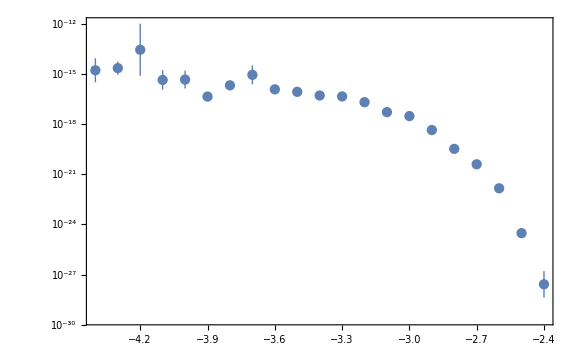

```mathematica
ListLogPlot[Table[{wlnMList[[i,1]],wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[wlnMList]}],Joined->False]
```

```mathematica
nTlnMList=Table[{nSlnMList[[i,1]]//Exp,nSlnMList[[i,2]]wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[nSlnMList]}];
```

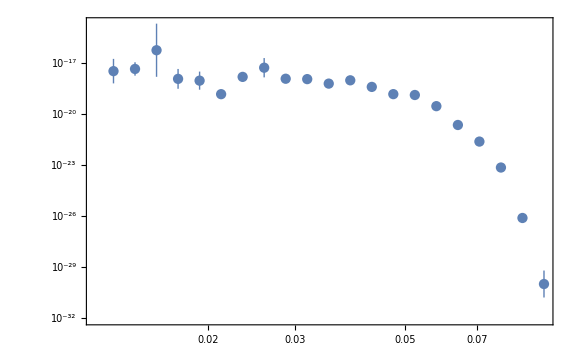

```mathematica
ListLogLogPlot[nTlnMList,Joined->False]
```

```mathematica
fPBHis=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMList];
```

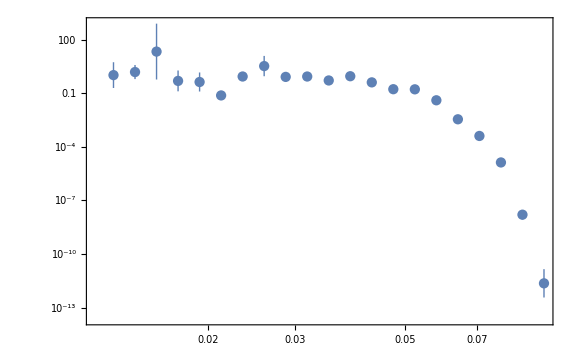

```mathematica
ListLogLogPlot[fPBHis,Joined->False]
```

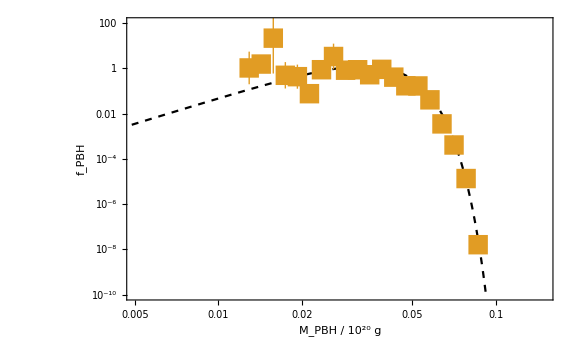

```mathematica
Show[ListLogLogPlot[Import["data/fPBH_pk_mono.csv"],PlotStyle->{Black,Dashed},FrameLabel->{"M_PBH / 10^20 g",Subscript[f, PBH]},PlotRange->{{0.005,0.15},{10^-10,10^2}},PlotLegends->Placed[LineLegend[{"Peak Theory"},LegendMarkerSize->20,LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.3,0.3}]],
ListLogLogPlot[fPBHis,Joined->False,PlotMarkers->Style["■",Color[2],20],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.3,0.3}]]]
```